```mathematica
a = {{1,-1,0,0},{1,0,-1,0},{1,0,0,-1},{0,1,-1,0},{0,1,0,-1},{0,0,1,-1}};
b={0.08,-0.09,-0.98,-0.18,-1.07,-0.89}
sol = LeastSquares[a,b]
```

{0.08,-0.09,-0.98,-0.18,-1.07,-0.89}

{-0.2475,-0.3325,-0.155,0.735}

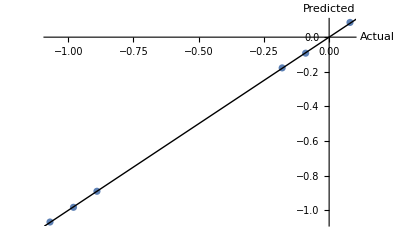

```mathematica
ListPlot[Thread[{b,a.sol}],AxesLabel->{"Actual","Predicted"},Epilog->Line[{{-1.5,-1.5},{1,1}}]]
```

```mathematica
lm=LinearModelFit[{a,b}];

lm[{"FitResiduals","RSquared"}]
```

```mathematica
{{-0.005000000000000102,0.0024999999999999745,0.0025000000000000577,-0.002499999999999919,-0.0024999999999999467,1.1102230246251565*^-16},0.999983018034847}
```

```mathematica
a = {{1,-1,0,0},{1,0,-1,0},{1,0,0,-1},{0,1,-1,0},{0,1,0,-1},{0,0,1,-1}};
b={0.08,-0.09,-0.98,-0.18,-1.07,-0.89}
sol = LeastSquares[a,b]
```

{0.08,-0.09,-0.98,-0.18,-1.07,-0.89}

{-0.2475,-0.3325,-0.155,0.735}

```mathematica
a = {{1,-1,0,0},{1,0,-1,0},{1,0,0,-1},{0,1,-1,0},{0,1,0,-1},{0,0,1,-1}};
b={0.36,0.31,0.35,-0.06,-0.02,0.04}
sol = LeastSquares[a,b]
```

{0.36,0.31,0.35,-0.06,-0.02,0.04}

{0.255,-0.11,-0.0525,-0.0925}

```mathematica
a = {{0,1,0,-1,0,0},{0,1,0,0,-1,0},{0,1,0,0,0,-1},{0,0,0,1,-1,0},{0,0,0,1,0,-1},{0,0,0,0,1,-1},{1,-1,0,0,0,0},{1,0,-1,0,0,0},{1,0,0,0,-1,0},{0,1,-1,0,0,0},{0,1,0,0,-1,0},{0,0,1,0,-1,0}};
b={0.08,-0.09,-0.98,-0.18,-1.07,-0.89,0.36,0.31,0.35,-0.06,-0.02,0.04};
sol = LeastSquares[a,b]
```

{0.154583,-0.229167,-0.152917,-0.332917,-0.174167,0.734583}

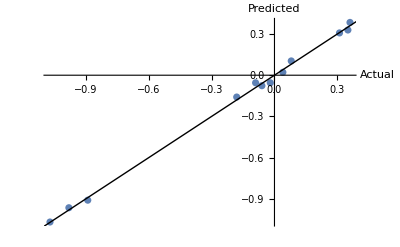

```mathematica
{0.15458333333333335,-0.22916666666666666,-0.15291666666666687,-0.3329166666666668,-0.17416666666666636,0.7345833333333331}

ListPlot[Thread[{b,a.sol}],AxesLabel->{"Actual","Predicted"},Epilog->Line[{{-1.5,-1.5},{1,1}}]]
```

```mathematica
a1=2
```

2

```mathematica
print a1
```

2 print

```mathematica
a1
```

2

```mathematica
CoefficientArrays[{a15-a23==0.0843334,a15-a25==-0.0917568,a15-a33==-0.981079,a23-a25==-0.17609,a23-a33==-1.06541,a25-a33==-0.889322,a16-a24==-0.19585,a16-a26==-0.190331,a16-a34==-0.0875159,a24-a26==0.00551874,a24-a34==0.108334,a26-a34==0.102815,a7-a15==0.364195,a7-a17==0.306347,a7-a25==0.348587,a15-a17==-0.0578479,a15-a25==-0.0156079,a17-a25==0.0422401,a6-a14==0.119508,a6-a16==0.0591289,a6-a24==-0.0186368,a14-a16==-0.0603796,a14-a24==-0.138145,a16-a24==-0.0777657,a5-a13==0.576924,a5-a15==1.17748,a5-a23==1.23644,a13-a15==0.600556,a13-a23==0.659519,a15-a23==0.0589626,a4-a12==-1.02319,a4-a14==-0.789614,a4-a22==-0.434247,a12-a14==0.233577,a12-a22==0.588944,a14-a22==0.355367,a13-a21==0.276206,a13-a23==-1.42867,a13-a31==0.544492,a21-a23==-1.70488,a21-a31==0.268285,a23-a31==1.97316,a14-a22==0.472406,a14-a24==0.603716,a14-a32==0.493063,a22-a24==0.13131,a22-a32==0.0206572,a24-a32==-0.110653,a23-a31==-1.87,a23-a33==-2.17,a23-a41==-0.65,a31-a33==-0.3,a31-a41==1.22,a33-a41==-1.52478,a25-a33==-1.13271,a25-a35==-0.941898,a25-a43==0.184221,a33-a35==0.190809,a33-a43==1.31693,a35-a43==1.12612,a24-a32==-0.070636,a24-a34==-0.114266,a24-a42==-0.0273668,a32-a34==-0.0436297,a32-a42==0.0432692,a34-a42==0.0868989,a22-a30==-0.0518516,a22-a32==-0.127361,a22-a40==-1.31011,a30-a32==-0.0755092,a30-a40==-1.25826,a32-a40==-1.18275},{a13,a14,a15,a16,a22,a23,a24,a25,a31,a32,a33,a34}]
```

{SparseArray[<72>, {72}],SparseArray[<102>, {72, 12}]}

```mathematica
eqns={a15-a23==0.0843334,a15-a25==-0.0917568,a15-a33==-0.981079,a23-a25==-0.17609,a23-a33==-1.06541,a25-a33==-0.889322,a16-a24==-0.19585,a16-a26==-0.190331,a16-a34==-0.0875159,a24-a26==0.00551874,a24-a34==0.108334,a26-a34==0.102815,a7-a15==0.364195,a7-a17==0.306347,a7-a25==0.348587,a15-a17==-0.0578479,a15-a25==-0.0156079,a17-a25==0.0422401,a6-a14==0.119508,a6-a16==0.0591289,a6-a24==-0.0186368,a14-a16==-0.0603796,a14-a24==-0.138145,a16-a24==-0.0777657,a5-a13==0.576924,a5-a15==1.17748,a5-a23==1.23644,a13-a15==0.600556,a13-a23==0.659519,a15-a23==0.0589626,a4-a12==-1.02319,a4-a14==-0.789614,a4-a22==-0.434247,a12-a14==0.233577,a12-a22==0.588944,a14-a22==0.355367,a13-a21==0.276206,a13-a23==-1.42867,a13-a31==0.544492,a21-a23==-1.70488,a21-a31==0.268285,a23-a31==1.97316,a14-a22==0.472406,a14-a24==0.603716,a14-a32==0.493063,a22-a24==0.13131,a22-a32==0.0206572,a24-a32==-0.110653,a23-a31==-1.87,a23-a33==-2.17,a23-a41==-0.65,a31-a33==-0.3,a31-a41==1.22,a33-a41==-1.52478,a25-a33==-1.13271,a25-a35==-0.941898,a25-a43==0.184221,a33-a35==0.190809,a33-a43==1.31693,a35-a43==1.12612,a24-a32==-0.070636,a24-a34==-0.114266,a24-a42==-0.0273668,a32-a34==-0.0436297,a32-a42==0.0432692,a34-a42==0.0868989,a22-a30==-0.0518516,a22-a32==-0.127361,a22-a40==-1.31011,a30-a32==-0.0755092,a30-a40==-1.25826,a32-a40==-1.18275};
```

```mathematica
{b,m}=CoefficientArrays[eqns,{a13,a14,a15,a16,a22,a23,a24,a25,a31,a32,a33,a34}]
```

{SparseArray[<59>, {59}],SparseArray[<79>, {59, 12}]}

```mathematica
LeastSquares[m,-b]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[SparseArray[<79>, {59, 12}],SparseArray[<59>, {59}]]

```mathematica
eqns={a15-a23==0.0843334,a15-a25==-0.0917568,a15-a33==-0.981079,a23-a25==-0.17609,a23-a33==-1.06541,a25-a33==-0.889322,a16-a24==-0.19585,a16-a26==-0.190331,a16-a34==-0.0875159,a24-a26==0.00551874,a24-a34==0.108334,a26-a34==0.102815,a7-a15==0.364195,a7-a17==0.306347,a7-a25==0.348587,a15-a17==-0.0578479,a15-a25==-0.0156079,a17-a25==0.0422401,a6-a14==0.119508,a6-a16==0.0591289,a6-a24==-0.0186368,a14-a16==-0.0603796,a14-a24==-0.138145,a16-a24==-0.0777657,a5-a13==0.576924,a5-a15==1.17748,a5-a23==1.23644,a13-a15==0.600556,a13-a23==0.659519,a15-a23==0.0589626,a4-a12==-1.02319,a4-a14==-0.789614,a4-a22==-0.434247,a12-a14==0.233577,a12-a22==0.588944,a14-a22==0.355367,a13-a21==0.276206,a13-a23==0.58,a13-a31==0.544492,a21-a23==0.30488,a21-a31==0.268285,a23-a31==0.02316,a14-a22==0.472406,a14-a24==0.603716,a14-a32==0.493063,a22-a24==0.13131,a22-a32==0.0206572,a24-a32==-0.110653,a23-a31==-1.87,a23-a33==-0.17,a23-a41==-0.65,a31-a33==-0.3,a31-a41==1.22,a33-a41==0.48478,a25-a33==-1.13271,a25-a35==-0.941898,a25-a43==0.184221,a33-a35==0.190809,a33-a43==0.68693,a35-a43==-0.82612,a24-a32==-0.070636,a24-a34==-0.114266,a24-a42==-0.0273668,a32-a34==-0.0436297,a32-a42==0.0432692,a34-a42==0.0868989,a22-a30==-0.0518516,a22-a32==-0.127361,a22-a40==0.61011,a30-a32==-0.0755092,a30-a40==0.75826,a32-a40==0.88275};
```

```mathematica
{b,m}=CoefficientArrays[eqns,{a4,a5,a6,a7,a12,a13,a14,a15,a16,a17,a21,a22,a23,a24,a25,a26,a30,a31,a32,a33,a34,a35,a40,a41,a42,a43}]
```

{SparseArray[<72>, {72}],SparseArray[<144>, {72, 26}]}

```mathematica
LeastSquares[m,b]
```

{-1.06413×10^7,1.84707×10^7,-1.06413×10^7,1.84707×10^7,-1.06413×10^7,1.84707×10^7,-1.06413×10^7,1.84707×10^7,-1.06413×10^7,1.84707×10^7,1.84707×10^7,-1.06413×10^7,1.84707×10^7,-1.06413×10^7,1.84707×10^7,-1.06413×10^7,-1.06413×10^7,1.84707×10^7,-1.06413×10^7,1.84707×10^7,-1.06413×10^7,1.84707×10^7,-1.06413×10^7,1.84707×10^7,-1.06413×10^7,1.84707×10^7}

```mathematica
a7-a8
```

a7-a8

```mathematica
a4-a5
```

a4-a5

```mathematica
{-5.556870927064566*^13,1.5010277443942912*^13,-5.556870927064634*^13,1.5010277443943676*^13,-5.556870927064668*^13,1.5010277443943787*^13,-5.556870927064642*^13,1.5010277443944045*^13,-5.556870927064618*^13,1.5010277443943982*^13,1.5010277443944365*^13,-5.556870927064609*^13,1.5010277443943887*^13,-5.55687092706462*^13,1.5010277443944021*^13,-5.55687092706463*^13,-5.556870927064611*^13,1.5010277443943709*^13,-5.556870927064618*^13,1.5010277443943086*^13,-5.556870927064623*^13,1.5010277443943182*^13,-5.556870927064738*^13,1.501027744394324*^13,-5.556870927064616*^13,1.5010277443944307*^13}

a5-a3
```

{-5.55687×10^13,1.50103×10^13,-5.55687×10^13,1.50103×10^13,-5.55687×10^13,1.50103×10^13,-5.55687×10^13,1.50103×10^13,-5.55687×10^13,1.50103×10^13,1.50103×10^13,-5.55687×10^13,1.50103×10^13,-5.55687×10^13,1.50103×10^13,-5.55687×10^13,-5.55687×10^13,1.50103×10^13,-5.55687×10^13,1.50103×10^13,-5.55687×10^13,1.50103×10^13,-5.55687×10^13,1.50103×10^13,-5.55687×10^13,1.50103×10^13}

-a3+a5

```mathematica
b1=5
```

5

```mathematica
0.08,-0.09,-0.98,-0.18,-1.07,-0.89
```

```mathematica
b2=5
```

5

```mathematica
b1-b2
```

0

```mathematica
eqns={a16-a24==0.2,a16-a26==0.19,a16-a34==0.09,a24-a26==-0.01,a24-a34==-0.11,a26-a34==-0.1};
{b,m}=CoefficientArrays[eqns,{a16,a24,a26,a34}];
LeastSquares[m,b]
```

{-0.12,0.08,0.07,-0.03}